1.1. The Pareto Distribution (PD) is a probability distribution that is used in many scientific disciplines. In any probability distribution you have a ‘random variable’ called X that can take on a range of values - in science this might be a measurement you take from an individual in a sample. In simple terms, in a PD the random variable has a much higher probability of taking on a lower value. Lets look at a PD in Histogram form. These distributions have 2 variables - a min-value and a shape. Here is the Histogram for min-value=1 and shape=0.5 where we have taken 10000 values for X. We see that the first bar nearly has a height of 500. We can say that when we take a value from this distribution that it has a probability of approximately 500/10000 of being in that first bar.

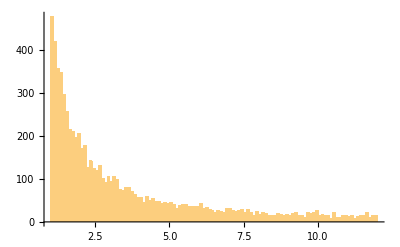

```mathematica
Histogram[Table[RandomVariate[ParetoDistribution[1,0.5]],{i,10000}], {1,12,0.1}]
```

1.2. Lets look at the shape variable and what happens as we change it. In this next Histogram we graph the changes to shape in the z axis. We can see that as shape increases the probable values of the random variable bunch up around the min-value which is always 1 in this case. We do see that even for large shape values we still get sparse high values for the random variable though.

```mathematica
Histogram3D[Flatten[Table[ Table[{RandomVariate[ParetoDistribution[1,j]],j},{i,1000}], {j,0.1,2.0,0.1}],1], {{0,100,1},{0,2,0.1}}]
```

-Graphics3D-

1.3. Lets look at min-value variable and what happens as we change it. In this next Histogram we graph the changes to min-value in the z axis. It is clear that the min-value doesn’t just act as a threshold below which the random variable cannot go. It changes the nature of how the values of the random variable are distributed. As the min-value variable goes up the values get more evenly spread out.

```mathematica
Histogram3D[Flatten[Table[ Table[{RandomVariate[ParetoDistribution[j,1]],j},{i,1000}], {j,0.1,10,0.1}],1], {{0,100,0.1},{0,10,0.1}}]
```

-Graphics3D-

1.4 So we can say that min-value and shape actually work against each other. Shape bunches things up as it gets bigger, min-value spreads them out as it gets bigger. To illustrate this we can draw a histogram in which both variables increase together. You can see that there is a cancelling out effect although its not perfect as there is still some more spread-outedness for smaller values.

```mathematica
Histogram3D[Flatten[Table[ Table[{RandomVariate[ParetoDistribution[j,j]],j},{i,1000}], {j,0.1,10,0.1}],1], {{0,100,0.1},{0,10,0.1}}]
```

-Graphics3D-